```mathematica
ClearAll["Global`*"]
```

```mathematica
tkin[a1_,a3_,I1_]:=(a1-a3)*I1^2;
tpot[a2_,a3_,I2_]:=(a2-a3)*I2^2;
aterm[moi_]:=1/(2*moi);
kindata[i1_,i3_,I_]:=Table[{I1,tkin[aterm[i1],aterm[i3],I1]},{I1,0,I,1}];
potdata[i2_,i3_,I_]:=Table[{I2,tpot[aterm[i2],aterm[i3],I2]},{I2,0,I,1}];
```

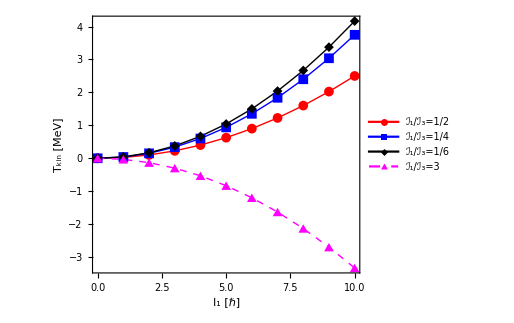

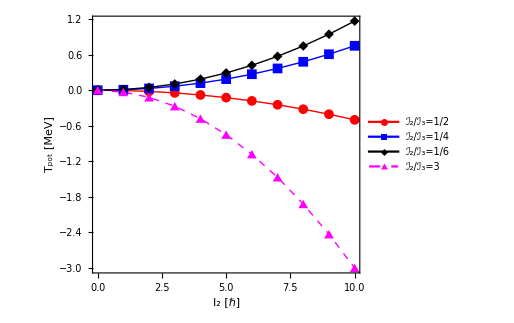

```mathematica
i1=10;
i2=45;
i3=60;
spin=10;
kinfig=ListPlot[{kindata[10,20,spin],kindata[10,40,spin],kindata[10,60,spin],kindata[30,10,spin]},Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.85,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Magenta, Thick,Dashed}},FrameLabel->{"I_1 [ℏ]","T_kin [MeV]"},LabelStyle->{17,Bold,Black,FontFamily->"Arial"},PlotRange->Full,ImageSize->380,PlotLegends->Placed[{"ℐ_1/ℐ_3=1/2","ℐ_1/ℐ_3=1/4","ℐ_1/ℐ_3=1/6","ℐ_1/ℐ_3=3"},{0.25,0.75}]];
Export["/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-hamiltonian-kin-pot/kin-pot-terms.pdf",kinfig];
Show[kinfig]
potfig=ListPlot[{potdata[25,20,spin],potdata[25,40,spin],potdata[25,60,spin],potdata[25,10,spin]},Frame->True,Axes->True,FrameStyle->Directive[Black,Thick],AspectRatio->0.85,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Magenta, Thick,Dashed}},FrameLabel->{"I_2 [ℏ]","T_pot [MeV]"},LabelStyle->{17,Bold,Black,FontFamily->"Arial"},PlotRange->Full,ImageSize->380,PlotLegends->Placed[{"ℐ_2/ℐ_3=1/2","ℐ_2/ℐ_3=1/4","ℐ_2/ℐ_3=1/6","ℐ_2/ℐ_3=3"},{0.25,0.25}]];
Export["/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/wobbling-hamiltonian-kin-pot/kin-pot-terms-2.pdf",potfig];
Show[potfig]
```